# Wolfram Workshop

## Capítulo 1

## 1. Ingreso de entradas y operaciones básicas

En Wolfram, puedes realizar cálculos simples y complejos.

```mathematica
2+2
```

4

```mathematica
5*3-7.5
```

7.5

```mathematica
(5-3)^(1+2)
```

8

```mathematica
((5-3)^(1+2))/4
```

2

```mathematica
(5-3)^(1+2)/4
```

2

## 2. Funciones incorporadas

Wolfram Language tiene miles de funciones incorporadas.

Máximo común divisor (GCD)

```mathematica
GCD[12,15]
```

3

Gráfico de una función seno

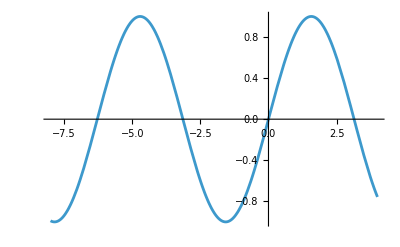

```mathematica
Plot[Sin[x],{x,-8,4}]
```

## 3. Listas y operaciones con listas

Las listas son colecciones ordenadas de elementos. Pueden contener números, variables, cálculos u otras listas.

Máximo común divisor (GCD)

```mathematica
{1,2,3}
```

{1,2,3}

Operaciones con listas

```mathematica
{1,2,3}+2
```

{3,4,5}

Extracción de elementos de una lista

```mathematica
{a,b,c,d}[[3]]
```

c

Creación de una lista con Range

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

## 4. Fracciones y decimales

Wolfram Language maneja fracciones y decimales de manera precisa.

Fracciones exactas

```mathematica
4/3
```

4/3

Simplificación de fracciones con Together

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

```mathematica
1/x+1/(x+1)+1/(x+2)+1/(x+3)
```

1/x+1/(1+x)+1/(2+x)+1/(3+x)

```mathematica
Together[1/x+1/(x+1)+1/(x+2)+1/(x+3)]
```

(2 (3+11 x+9 x^2+2 x^3))/(x (1+x) (2+x) (3+x))

Conversión a decimales con N

```mathematica
N[4/3]
```

1.33333

Notación científica

```mathematica
ScientificForm[0.00123]
```

1.23×10^-3

## 5. Variables y funciones

Puedes definir variables y funciones personalizadas en Wolfram Language.

Asignación de variables

```mathematica
x=2
1+2x
```

2

5

Borrado de variables

```mathematica
Clear[x]
1+2x
```

1+2 x

```mathematica
x
```

x

Definición de funciones

```mathematica
f[x_]:=1+2x
```

```mathematica
f[x]
f[2]
```

1+2 x

5

Sustitución en expresiones (/.)

```mathematica
1+2x/. x->2
```

5

```mathematica
x^2+7/. x->2
```

11

## ejercicios

### 1. Calcula el resultado de la siguiente expresión:

(3+5)(2-4)^2

```mathematica
(3+5)(2-4)^2
```

32

### 2. Crea una lista con los números del 1 al 20 y luego suma 5 a cada elemento de la lista.

```mathematica
Range[20]+5
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

### 3. Define una función que calcule el cuadrado de un número y luego aplícala al número 7.

```mathematica
f[x_]:=x^2
f[7]
```

49

### 4. Grafica la función coseno desde -10 hasta 10.

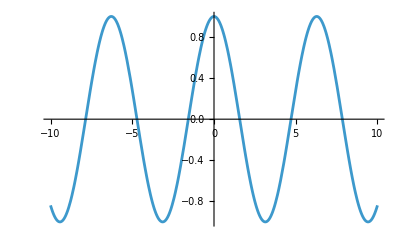

```mathematica
Plot[Cos[x], {x,-10,10}]
```

### 5. Calcula el máximo común divisor (GCD) de 24 y 36.

```mathematica
GCD[24,36]
```

12